```mathematica
ClearAll["Global`*"]
```

```mathematica
mesh="/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/solution/vertices.csv";
outputpath="/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/input/";
```

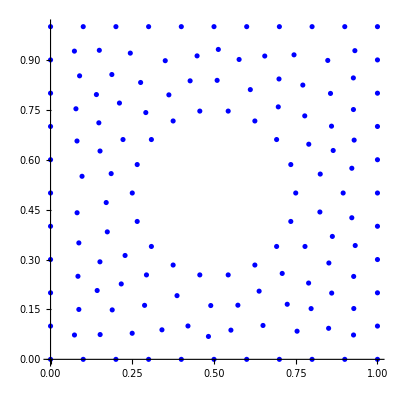

141

```mathematica
tabve=Import[mesh];
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}];
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write a scalar on csv file by interpolating it on the mesh*)
```

```mathematica
ϕ[x_,y_]:=Cos[2π(x-y)]
```

```mathematica
tabϕ=Table[{ϕ[x,y]/.{x->tabve[[i,1]],y->tabve[[i,2]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabϕ,{"f",":0",":1",":2"}]
```

```mathematica
outputpath<>"phi.csv"
```

/home/fenics/shared/read_write/read_fields/input/phi.csv

```mathematica
Export[outputpath<>"phi.csv",tabϕ]
```

/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/input/phi.csv